## G=7 models

### Setup

```mathematica
SetDirectory@ParentDirectory@NotebookDirectory[];
<<QuiverGaugeTheory`
<<InterfaceM2`
```

```mathematica
Get@FileNameJoin[{NotebookDirectory[],"functions.wl"}]
$ImportData=True;
$DataDirectory=FileNameJoin[{NotebookDirectory[],"data"}];
$FiguresDirectory=FileNameJoin[{NotebookDirectory[],"figures"}];
ParseEPS[x_]:=StringReplace[ExportString[x,"EPS"],"3.25 M"->"25.0 M"];
ExportEPS[n_,x_]:=Export[n,ParseEPS[x],"Text"];
```

### Model 5: PdP_(4b)

```mathematica
WPdP4b=-(Subscript[X, 1][1,3]·Subscript[X, 1][3,7]·Subscript[X, 1][7,1])-Subscript[X, 1][1,6]·Subscript[X, 1][6,2]·Subscript[X, 1][2,1]+Subscript[X, 1][1,6]·Subscript[X, 1][6,7]·Subscript[X, 1][7,1]+Subscript[X, 1][1,7]·Subscript[X, 1][7,2]·Subscript[X, 1][2,1]-Subscript[X, 1][1,7]·Subscript[X, 1][7,5]·Subscript[X, 1][5,1]+Subscript[X, 1][2,5]·Subscript[X, 1][5,6]·Subscript[X, 1][6,2]+Subscript[X, 1][2,6]·Subscript[X, 1][6,4]·Subscript[X, 1][4,2]-Subscript[X, 1][2,6]·Subscript[X, 1][6,7]·Subscript[X, 1][7,2]+Subscript[X, 1][3,7]·Subscript[X, 1][7,5]·Subscript[X, 1][5,3]-Subscript[X, 1][4,5]·Subscript[X, 1][5,6]·Subscript[X, 1][6,4]+Subscript[X, 1][1,3]·Subscript[X, 1][3,4]·Subscript[X, 1][4,5]·Subscript[X, 1][5,1]-Subscript[X, 1][2,5]·Subscript[X, 1][5,3]·Subscript[X, 1][3,4]·Subscript[X, 1][4,2];
```

```mathematica
PdP4b=Model["PdP4b","Descriptions"->{"PdP"},"Potential"->WPdP4b,"QuiverPositioning"->{2,5,1,7,3,4,6}];
```

### Model 6: PdP_(4a)

```mathematica
WPdP4aPhaseA=-(Subscript[X, 1][1,7]·Subscript[X, 1][7,6]·Subscript[X, 1][6,1])+Subscript[X, 1][2,7]·Subscript[X, 1][7,3]·Subscript[X, 1][3,2]+Subscript[X, 1][1,4]·Subscript[X, 1][4,5]·Subscript[X, 1][5,6]·Subscript[X, 1][6,1]-Subscript[X, 1][1,4]·Subscript[X, 1][4,7]·Subscript[X, 1][7,3]·Subscript[X, 1][3,1]+Subscript[X, 1][1,7]·Subscript[X, 1][7,5]·Subscript[X, 1][5,3]·Subscript[X, 1][3,1]-Subscript[X, 1][2,4]·Subscript[X, 1][4,5]·Subscript[X, 1][5,3]·Subscript[X, 1][3,2]+Subscript[X, 1][2,4]·Subscript[X, 1][4,7]·Subscript[X, 1][7,6]·Subscript[X, 1][6,2]-Subscript[X, 1][2,7]·Subscript[X, 1][7,5]·Subscript[X, 1][5,6]·Subscript[X, 1][6,2];
```

```mathematica
WPdP4aPhaseB=-(Subscript[X, 1][1,7]·Subscript[X, 1][7,6]·Subscript[X, 1][6,1])+Subscript[X, 1][2,3]·Subscript[X, 1][3,4]·Subscript[X, 1][4,2]-Subscript[X, 1][2,6]·Subscript[X, 1][6,4]·Subscript[X, 1][4,2]+Subscript[X, 1][2,6]·Subscript[X, 1][6,7]·Subscript[X, 1][7,2]-Subscript[X, 1][3,4]·Subscript[X, 1][4,5]·Subscript[X, 1][5,3]+Subscript[X, 1][4,7]·Subscript[X, 1][7,6]·Subscript[X, 1][6,4]-Subscript[X, 1][5,6]·Subscript[X, 1][6,7]·Subscript[X, 1][7,5]+Subscript[X, 1][1,4]·Subscript[X, 1][4,5]·Subscript[X, 1][5,6]·Subscript[X, 1][6,1]+Subscript[X, 1][1,7]·Subscript[X, 1][7,5]·Subscript[X, 1][5,3]·Subscript[X, 1][3,1]-Subscript[X, 1][1,4]·Subscript[X, 1][4,7]·Subscript[X, 1][7,2]·Subscript[X, 1][2,3]·Subscript[X, 1][3,1];
```

```mathematica
WPdP4aPhaseC=-(Subscript[X, 1][1,3]·Subscript[X, 1][3,7]·Subscript[X, 1][7,1])+Subscript[X, 1][1,3]·Subscript[X, 2][3,4]·Subscript[X, 1][4,1]-Subscript[X, 1][1,6]·Subscript[X, 2][6,4]·Subscript[X, 1][4,1]+Subscript[X, 1][2,3]·Subscript[X, 1][3,4]·Subscript[X, 1][4,2]-Subscript[X, 1][2,6]·Subscript[X, 1][6,4]·Subscript[X, 1][4,2]+Subscript[X, 1][2,6]·Subscript[X, 1][6,7]·Subscript[X, 1][7,2]-Subscript[X, 1][3,4]·Subscript[X, 1][4,5]·Subscript[X, 1][5,3]+Subscript[X, 1][3,7]·Subscript[X, 1][7,5]·Subscript[X, 1][5,3]+Subscript[X, 1][4,5]·Subscript[X, 1][5,6]·Subscript[X, 2][6,4]-Subscript[X, 1][5,6]·Subscript[X, 1][6,7]·Subscript[X, 1][7,5]+Subscript[X, 1][1,6]·Subscript[X, 1][6,4]·Subscript[X, 1][4,7]·Subscript[X, 1][7,1]-Subscript[X, 1][2,3]·Subscript[X, 2][3,4]·Subscript[X, 1][4,7]·Subscript[X, 1][7,2];
```

```mathematica
PdP4aPhaseA=Model[{"PdP4a","PhaseA"},"Potential"->WPdP4aPhaseA,"QuiverPositioning"->{4,7,5,{3,6},{1,2}}];
PdP4aPhaseB=Model[{"PdP4a","PhaseB"},"Potential"->WPdP4aPhaseB,"QuiverPositioning"->{{2,5},3,1,7,6,4}];
PdP4aPhaseC=Model[{"PdP4a","PhaseC"},"Potential"->WPdP4aPhaseC,"QuiverPositioning"->{{6,3},7,4,{1,2,5}}];
```

## Deformations

### PdP_(4b) ⟹ PdP_(4a) (a)

#### Deformation 1: (1→7→1) – (2→6→2)

```mathematica
Clear[WPdP4bDef1];
δWPdP4bDef1=m (Subscript[X, 1][1,7]·Subscript[X, 1][7,1]-Subscript[X, 1][2,6]·Subscript[X, 1][6,2]);
WPdP4bDef1=WPdP4b+δWPdP4bDef1;
```

```mathematica
Clear[WPdP4bDef1Min];
massiveFieldsFrom[WPdP4bDef1]
WPdP4bDef1Min=WPdP4bDef1/.Last@Solve[DG[WPdP4bDef1,{%}]==0,%]//Expand
```

{X_1[1,7],X_1[2,6],X_1[6,2],X_1[7,1]}

X_1[3,7]·X_1[7,5]·X_1[5,3]-X_1[4,5]·X_1[5,6]·X_1[6,4]+X_1[1,3]·X_1[3,4]·X_1[4,5]·X_1[5,1]+(X_1[1,3]·X_1[3,7]·X_1[7,2]·X_1[2,1])/m-(X_1[1,3]·X_1[3,7]·X_1[7,5]·X_1[5,1])/m-(X_1[1,6]·X_1[6,4]·X_1[4,2]·X_1[2,1])/m+(X_1[1,6]·X_1[6,7]·X_1[7,5]·X_1[5,1])/m-X_1[2,5]·X_1[5,3]·X_1[3,4]·X_1[4,2]+(X_1[2,5]·X_1[5,6]·X_1[6,4]·X_1[4,2])/m-(X_1[2,5]·X_1[5,6]·X_1[6,7]·X_1[7,2])/m

```mathematica
Clear[RedefChoice1,RedefRules1]
RedefChoice1={Subscript[β, 1][4,5]->1/m,Subscript[β, 1][5,3]->1/m,Subscript[α, 1][5,3]->-1/m,Subscript[α, 1][4,5]->-1/m};
RedefRules1=FieldRedefinition[{Subscript[X, 1][4,5],Subscript[X, 1][5,3]},QuiverFromFields@WPdP4b,2]//.RedefChoice1;
RedefRules1Mass= {Subscript[X, 1][5,1]->m Subscript[X, 1][5,1],Subscript[X, 1][5,3]->m Subscript[X, 1][5,3],Subscript[X, 1][6,4]->m Subscript[X, 1][6,4],Subscript[X, 1][7,2]->m Subscript[X, 1][7,2]};
RedefRules1//Column
RedefRules1Mass//Column
```

X_1[4,5]→(X_1[4,2]·X_1[2,5])/m-X_1[4,5]/m
X_1[5,3]→(X_1[5,1]·X_1[1,3])/m-X_1[5,3]/m

X_1[5,1]→m X_1[5,1]
X_1[5,3]→m X_1[5,3]
X_1[6,4]→m X_1[6,4]
X_1[7,2]→m X_1[7,2]

```mathematica
DG[FieldCases[RedefRules1]/.RedefRules1,{FieldCases[RedefRules1]}]/.{Untrace->1}//Det
```

1/m^2

```mathematica
WPdP4bDef1Min/.RedefRules1/.RedefRules1Mass//FTermsTable
```

X_1[1,3] | X_1[3,4]·X_1[4,5]·X_1[5,1] -1+X_1[3,7]·X_1[7,2]·X_1[2,1] 1 | 0 | 2
X_1[1,6] | X_1[6,4]·X_1[4,2]·X_1[2,1] -1+X_1[6,7]·X_1[7,5]·X_1[5,1] 1 | 0 | 2
X_1[2,1] | X_1[1,6]·X_1[6,4]·X_1[4,2] -1+X_1[1,3]·X_1[3,7]·X_1[7,2] 1 | 0 | 2
X_1[2,5] | X_1[5,6]·X_1[6,7]·X_1[7,2] -1+X_1[5,3]·X_1[3,4]·X_1[4,2] 1 | 0 | 2
X_1[3,4] | X_1[4,5]·X_1[5,1]·X_1[1,3] -1+X_1[4,2]·X_1[2,5]·X_1[5,3] 1 | 0 | 2
X_1[3,7] | X_1[7,5]·X_1[5,3] -1+X_1[7,2]·X_1[2,1]·X_1[1,3] 1 | 0 | 2
X_1[4,2] | X_1[2,1]·X_1[1,6]·X_1[6,4] -1+X_1[2,5]·X_1[5,3]·X_1[3,4] 1 | 0 | 2
X_1[4,5] | X_1[5,1]·X_1[1,3]·X_1[3,4] -1+X_1[5,6]·X_1[6,4] 1 | 0 | 2
X_1[5,1] | X_1[1,3]·X_1[3,4]·X_1[4,5] -1+X_1[1,6]·X_1[6,7]·X_1[7,5] 1 | 0 | 2
X_1[5,3] | X_1[3,7]·X_1[7,5] -1+X_1[3,4]·X_1[4,2]·X_1[2,5] 1 | 0 | 2
X_1[5,6] | X_1[6,7]·X_1[7,2]·X_1[2,5] -1+X_1[6,4]·X_1[4,5] 1 | 0 | 2
X_1[6,4] | X_1[4,2]·X_1[2,1]·X_1[1,6] -1+X_1[4,5]·X_1[5,6] 1 | 0 | 2
X_1[6,7] | X_1[7,2]·X_1[2,5]·X_1[5,6] -1+X_1[7,5]·X_1[5,1]·X_1[1,6] 1 | 0 | 2
X_1[7,2] | X_1[2,5]·X_1[5,6]·X_1[6,7] -1+X_1[2,1]·X_1[1,3]·X_1[3,7] 1 | 0 | 2
X_1[7,5] | X_1[5,3]·X_1[3,7] -1+X_1[5,1]·X_1[1,6]·X_1[6,7] 1 | 0 | 2

```mathematica
WPdP4aAFromDef1=Simplify[WPdP4bDef1Min/.RedefRules1/.RedefRules1Mass];
```

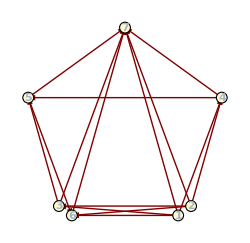
-Graphics--Graphics-

X_1[1,7]·X_1[7,6]·X_1[6,1] 1-a+X_1[1,4]·X_1[4,7]·X_1[7,3]·X_1[3,1] 1-a+X_1[2,4]·X_1[4,5]·X_1[5,3]·X_1[3,2] 1-a+X_1[2,7]·X_1[7,5]·X_1[5,6]·X_1[6,2] 1-a+X_1[2,7]·X_1[7,3]·X_1[3,2] -1+a+X_1[1,4]·X_1[4,5]·X_1[5,6]·X_1[6,1] -1+a+X_1[1,7]·X_1[7,5]·X_1[5,3]·X_1[3,1] -1+a+X_1[2,4]·X_1[4,7]·X_1[7,6]·X_1[6,2] -1+a

```mathematica
Row[{
QuiverGraph[{4,7,5,{3,6},{1,2}},Quiver[PdP4aPhaseA]],
(WPdP4aAFromDef1/.ChangeGroupIndices[{5,4,3,1,7,6,2}])//QuiverGraph[{4,7,5,{3,6},{1,2}},#]&
}]
a W[PdP4aPhaseA]+(WPdP4aAFromDef1/.ChangeGroupIndices[{5,4,3,1,7,6,2}])//Expand@Collect[Simplify@Expand@#,_CenterDot,Highlighted]&
```

### PdP_(4b) ⟹ PdP_(4a) (b) (arrows reversed)

#### Deformation 2: (1→7→1) – (3→4→5→3)

```mathematica
Clear[WPdP4bDef2];
δWPdP4bDef2=m (Subscript[X, 1][1,7]·Subscript[X, 1][7,1]-Subscript[X, 1][3,4]·Subscript[X, 1][4,5]·Subscript[X, 1][5,3]);
WPdP4bDef2=W[PdP4b]+δWPdP4bDef2;
```

```mathematica
Clear[WPdP4bDef2Min];
massiveFieldsFrom[WPdP4bDef2]
WPdP4bDef2Min=WPdP4bDef2/.Last@Solve[DG[WPdP4bDef2,{%}]==0,%]//Expand
```

{X_1[1,7],X_1[7,1]}

-(X_1[1,6]·X_1[6,2]·X_1[2,1])+X_1[2,5]·X_1[5,6]·X_1[6,2]+X_1[2,6]·X_1[6,4]·X_1[4,2]-X_1[2,6]·X_1[6,7]·X_1[7,2]-m X_1[3,4]·X_1[4,5]·X_1[5,3]+X_1[3,7]·X_1[7,5]·X_1[5,3]-X_1[4,5]·X_1[5,6]·X_1[6,4]+X_1[1,3]·X_1[3,4]·X_1[4,5]·X_1[5,1]+(X_1[1,3]·X_1[3,7]·X_1[7,2]·X_1[2,1])/m-(X_1[1,3]·X_1[3,7]·X_1[7,5]·X_1[5,1])/m-(X_1[1,6]·X_1[6,7]·X_1[7,2]·X_1[2,1])/m+(X_1[1,6]·X_1[6,7]·X_1[7,5]·X_1[5,1])/m-X_1[2,5]·X_1[5,3]·X_1[3,4]·X_1[4,2]

```mathematica
Clear[RedefChoice2,RedefRules2]
RedefChoice2={Subscript[β, 1][5,3]->1/m,Subscript[α, 1][5,3]->-1/m,Subscript[β, 1][4,5]->-1/m,Subscript[γ, 1][2,6]->Subscript[γ, 1][6,2],Subscript[γ, 1][6,2]->-1/m-Subscript[β, 1][2,6],Subscript[β, 1][6,2]->Subscript[β, 1][2,6],Subscript[α, 1][6,2]->1/m,Subscript[α, 1][4,5]->1/m,Subscript[α, 1][2,6]->1/m};
RedefRules2=FieldRedefinition[{Subscript[X, 1][4,5],Subscript[X, 1][5,3],Subscript[X, 1][2,6],Subscript[X, 1][6,2]},QuiverFromFields@WPdP4b,2]//.RedefChoice2;
RedefRules2Mass= {Subscript[X, 1][5,1]->m Subscript[X, 1][5,1],Subscript[X, 1][5,3]->m Subscript[X, 1][5,3],Subscript[X, 1][6,2]->m Subscript[X, 1][6,2],Subscript[X, 1][6,4]->m Subscript[X, 1][6,4],Subscript[X, 1][7,2]->m Subscript[X, 1][7,2]};
RedefRules2//Column
RedefRules2Mass//Column
```

X_1[4,5]→-(X_1[4,2]·X_1[2,5])/m+X_1[4,5]/m
X_1[5,3]→(X_1[5,1]·X_1[1,3])/m-X_1[5,3]/m
X_1[2,6]→X_1[2,1]·X_1[1,6] (-1/m-β_1[2,6])+X_1[2,5]·X_1[5,6] β_1[2,6]+X_1[2,6]/m
X_1[6,2]→X_1[6,4]·X_1[4,2] (-1/m-β_1[2,6])+X_1[6,7]·X_1[7,2] β_1[2,6]+X_1[6,2]/m

X_1[5,1]→m X_1[5,1]
X_1[5,3]→m X_1[5,3]
X_1[6,2]→m X_1[6,2]
X_1[6,4]→m X_1[6,4]
X_1[7,2]→m X_1[7,2]

```mathematica
DG[FieldCases[RedefRules2]/.RedefRules2,{FieldCases[RedefRules2]}]/.{Untrace->1}//Det
```

-1/m^4

```mathematica
WPdP4bDef2Min/.RedefRules2/.RedefRules2Mass//FTermsTable
```

X_1[1,3] | X_1[3,4]·X_1[4,2]·X_1[2,5]·X_1[5,1] -1+X_1[3,7]·X_1[7,2]·X_1[2,1] 1 | 0 | 2
X_1[1,6] | X_1[6,2]·X_1[2,1] -1+X_1[6,7]·X_1[7,5]·X_1[5,1] 1 | 0 | 2
X_1[2,1] | X_1[1,6]·X_1[6,2] -1+X_1[1,3]·X_1[3,7]·X_1[7,2] 1 | 0 | 2
X_1[2,5] | X_1[5,1]·X_1[1,3]·X_1[3,4]·X_1[4,2] -1+X_1[5,6]·X_1[6,2] 1 | 0 | 2
X_1[2,6] | X_1[6,7]·X_1[7,2] -1+X_1[6,4]·X_1[4,2] 1 | 0 | 2
X_1[3,4] | X_1[4,2]·X_1[2,5]·X_1[5,1]·X_1[1,3] -1+X_1[4,5]·X_1[5,3] 1 | 0 | 2
X_1[3,7] | X_1[7,5]·X_1[5,3] -1+X_1[7,2]·X_1[2,1]·X_1[1,3] 1 | 0 | 2
X_1[4,2] | X_1[2,5]·X_1[5,1]·X_1[1,3]·X_1[3,4] -1+X_1[2,6]·X_1[6,4] 1 | 0 | 2
X_1[4,5] | X_1[5,6]·X_1[6,4] -1+X_1[5,3]·X_1[3,4] 1 | 0 | 2
X_1[5,1] | X_1[1,3]·X_1[3,4]·X_1[4,2]·X_1[2,5] -1+X_1[1,6]·X_1[6,7]·X_1[7,5] 1 | 0 | 2
X_1[5,3] | X_1[3,7]·X_1[7,5] -1+X_1[3,4]·X_1[4,5] 1 | 0 | 2
X_1[5,6] | X_1[6,4]·X_1[4,5] -1+X_1[6,2]·X_1[2,5] 1 | 0 | 2
X_1[6,2] | X_1[2,1]·X_1[1,6] -1+X_1[2,5]·X_1[5,6] 1 | 0 | 2
X_1[6,4] | X_1[4,5]·X_1[5,6] -1+X_1[4,2]·X_1[2,6] 1 | 0 | 2
X_1[6,7] | X_1[7,2]·X_1[2,6] -1+X_1[7,5]·X_1[5,1]·X_1[1,6] 1 | 0 | 2
X_1[7,2] | X_1[2,6]·X_1[6,7] -1+X_1[2,1]·X_1[1,3]·X_1[3,7] 1 | 0 | 2
X_1[7,5] | X_1[5,3]·X_1[3,7] -1+X_1[5,1]·X_1[1,6]·X_1[6,7] 1 | 0 | 2

```mathematica
WPdP4aBFromDef2=Simplify[WPdP4bDef2Min/.RedefRules2/.RedefRules2Mass]
```

-(X_1[1,6]·X_1[6,2]·X_1[2,1])+X_1[2,5]·X_1[5,6]·X_1[6,2]+X_1[2,6]·X_1[6,4]·X_1[4,2]-X_1[2,6]·X_1[6,7]·X_1[7,2]+X_1[3,4]·X_1[4,5]·X_1[5,3]-X_1[3,7]·X_1[7,5]·X_1[5,3]-X_1[4,5]·X_1[5,6]·X_1[6,4]+X_1[1,3]·X_1[3,7]·X_1[7,2]·X_1[2,1]+X_1[1,6]·X_1[6,7]·X_1[7,5]·X_1[5,1]-X_1[1,3]·X_1[3,4]·X_1[4,2]·X_1[2,5]·X_1[5,1]

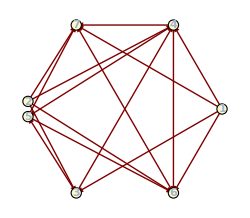
-Graphics--Graphics-

```mathematica
Row[{
QuiverGraph[Automatic,QuiverFromFields@WPdP4aPhaseB],
(WPdP4aBFromDef2/.{Subscript[X, k_][i_,j_]:>Subscript[X, k][j,i]}/.ChangeGroupIndices[{1,7,3,2,4,6,5}])//QuiverGraph
}]
```

```mathematica
a WPdP4aPhaseB+(WPdP4aBFromDef2/.{c_CenterDot:>Reverse[c]}/.{Subscript[X, k_][i_,j_]:>Subscript[X, k][j,i]}/.ChangeGroupIndices[{1,7,3,2,4,6,5}])//Expand//Simplify//Collect[#,c_CenterDot,Highlighted]&
```

X_1[1,7]·X_1[7,6]·X_1[6,1] -1-a+X_1[2,6]·X_1[6,4]·X_1[4,2] -1-a+X_1[3,4]·X_1[4,5]·X_1[5,3] -1-a+X_1[5,6]·X_1[6,7]·X_1[7,5] -1-a+X_1[1,4]·X_1[4,7]·X_1[7,2]·X_1[2,3]·X_1[3,1] -1-a+X_1[2,3]·X_1[3,4]·X_1[4,2] 1+a+X_1[2,6]·X_1[6,7]·X_1[7,2] 1+a+X_1[4,7]·X_1[7,6]·X_1[6,4] 1+a+X_1[1,4]·X_1[4,5]·X_1[5,6]·X_1[6,1] 1+a+X_1[1,7]·X_1[7,5]·X_1[5,3]·X_1[3,1] 1+a

### PdP_(4b) ⟹ PdP_(4a) (b)

#### Deformation 3: (2→6→2) – (3→4→5→3)

```mathematica
Clear[WPdP4bDef3];
δWPdP4bDef3=m (Subscript[X, 1][2,6]·Subscript[X, 1][6,2]-Subscript[X, 1][3,4]·Subscript[X, 1][4,5]·Subscript[X, 1][5,3]);
WPdP4bDef3=WPdP4b+δWPdP4bDef3;
```

```mathematica
Clear[WPdP4bDef3Min];
massiveFieldsFrom[WPdP4bDef3]
WPdP4bDef3Min=WPdP4bDef3/.Last@Solve[DG[WPdP4bDef3,{%}]==0,%]//Expand
```

{X_1[2,6],X_1[6,2]}

-(X_1[1,3]·X_1[3,7]·X_1[7,1])+X_1[1,6]·X_1[6,7]·X_1[7,1]+X_1[1,7]·X_1[7,2]·X_1[2,1]-X_1[1,7]·X_1[7,5]·X_1[5,1]-m X_1[3,4]·X_1[4,5]·X_1[5,3]+X_1[3,7]·X_1[7,5]·X_1[5,3]-X_1[4,5]·X_1[5,6]·X_1[6,4]+X_1[1,3]·X_1[3,4]·X_1[4,5]·X_1[5,1]+(X_1[1,6]·X_1[6,4]·X_1[4,2]·X_1[2,1])/m-(X_1[1,6]·X_1[6,7]·X_1[7,2]·X_1[2,1])/m-X_1[2,5]·X_1[5,3]·X_1[3,4]·X_1[4,2]-(X_1[2,5]·X_1[5,6]·X_1[6,4]·X_1[4,2])/m+(X_1[2,5]·X_1[5,6]·X_1[6,7]·X_1[7,2])/m

```mathematica
Clear[RedefChoice3,RedefRules3]
RedefChoice3={Subscript[γ, 1][1,7]->Subscript[γ, 1][7,1],Subscript[β, 1][1,7]->Subscript[β, 1][7,1],Subscript[γ, 1][7,1]->1/m-Subscript[β, 1][7,1],Subscript[α, 1][1,7]->-1/m,Subscript[α, 1][7,1]->-1/m,Subscript[β, 1][5,3]->1/m,Subscript[α, 1][5,3]->-1/m,Subscript[β, 1][4,5]->-1/m,Subscript[α, 1][4,5]->1/m};
RedefRules3=FieldRedefinition[{Subscript[X, 1][1,7], Subscript[X, 1][7,1],Subscript[X, 1][4,5],Subscript[X, 1][5,3]},QuiverFromFields@WPdP4b,2]//.RedefChoice3;
RedefRules3Mass= {Subscript[X, 1][5,1]->m Subscript[X, 1][5,1],Subscript[X, 1][5,3]->m Subscript[X, 1][5,3],Subscript[X, 1][6,4]->m Subscript[X, 1][6,4],Subscript[X, 1][7,1]->m Subscript[X, 1][7,1],Subscript[X, 1][7,2]->m Subscript[X, 1][7,2]};
RedefRules3//Column
RedefRules3Mass//Column
```

X_1[1,7]→X_1[1,3]·X_1[3,7] (1/m-β_1[7,1])+X_1[1,6]·X_1[6,7] β_1[7,1]-X_1[1,7]/m
X_1[7,1]→X_1[7,2]·X_1[2,1] (1/m-β_1[7,1])+X_1[7,5]·X_1[5,1] β_1[7,1]-X_1[7,1]/m
X_1[4,5]→-(X_1[4,2]·X_1[2,5])/m+X_1[4,5]/m
X_1[5,3]→(X_1[5,1]·X_1[1,3])/m-X_1[5,3]/m

X_1[5,1]→m X_1[5,1]
X_1[5,3]→m X_1[5,3]
X_1[6,4]→m X_1[6,4]
X_1[7,1]→m X_1[7,1]
X_1[7,2]→m X_1[7,2]

```mathematica
DG[FieldCases[RedefRules3]/.RedefRules3,{FieldCases[RedefRules3]}]/.{Untrace->1}//Det
```

-1/m^4

```mathematica
WPdP4bDef3Min/.RedefRules3/.RedefRules3Mass//FTermsTable
```

X_1[1,3] | X_1[3,4]·X_1[4,2]·X_1[2,5]·X_1[5,1] -1+X_1[3,7]·X_1[7,1] 1 | 0 | 2
X_1[1,6] | X_1[6,7]·X_1[7,1] -1+X_1[6,4]·X_1[4,2]·X_1[2,1] 1 | 0 | 2
X_1[1,7] | X_1[7,2]·X_1[2,1] -1+X_1[7,5]·X_1[5,1] 1 | 0 | 2
X_1[2,1] | X_1[1,7]·X_1[7,2] -1+X_1[1,6]·X_1[6,4]·X_1[4,2] 1 | 0 | 2
X_1[2,5] | X_1[5,1]·X_1[1,3]·X_1[3,4]·X_1[4,2] -1+X_1[5,6]·X_1[6,7]·X_1[7,2] 1 | 0 | 2
X_1[3,4] | X_1[4,2]·X_1[2,5]·X_1[5,1]·X_1[1,3] -1+X_1[4,5]·X_1[5,3] 1 | 0 | 2
X_1[3,7] | X_1[7,5]·X_1[5,3] -1+X_1[7,1]·X_1[1,3] 1 | 0 | 2
X_1[4,2] | X_1[2,5]·X_1[5,1]·X_1[1,3]·X_1[3,4] -1+X_1[2,1]·X_1[1,6]·X_1[6,4] 1 | 0 | 2
X_1[4,5] | X_1[5,6]·X_1[6,4] -1+X_1[5,3]·X_1[3,4] 1 | 0 | 2
X_1[5,1] | X_1[1,3]·X_1[3,4]·X_1[4,2]·X_1[2,5] -1+X_1[1,7]·X_1[7,5] 1 | 0 | 2
X_1[5,3] | X_1[3,7]·X_1[7,5] -1+X_1[3,4]·X_1[4,5] 1 | 0 | 2
X_1[5,6] | X_1[6,4]·X_1[4,5] -1+X_1[6,7]·X_1[7,2]·X_1[2,5] 1 | 0 | 2
X_1[6,4] | X_1[4,5]·X_1[5,6] -1+X_1[4,2]·X_1[2,1]·X_1[1,6] 1 | 0 | 2
X_1[6,7] | X_1[7,1]·X_1[1,6] -1+X_1[7,2]·X_1[2,5]·X_1[5,6] 1 | 0 | 2
X_1[7,1] | X_1[1,6]·X_1[6,7] -1+X_1[1,3]·X_1[3,7] 1 | 0 | 2
X_1[7,2] | X_1[2,1]·X_1[1,7] -1+X_1[2,5]·X_1[5,6]·X_1[6,7] 1 | 0 | 2
X_1[7,5] | X_1[5,3]·X_1[3,7] -1+X_1[5,1]·X_1[1,7] 1 | 0 | 2

```mathematica
WPdP4aBFromDef3=Simplify[WPdP4bDef3Min/.RedefRules3/.RedefRules3Mass]
```

X_1[1,3]·X_1[3,7]·X_1[7,1]-X_1[1,6]·X_1[6,7]·X_1[7,1]-X_1[1,7]·X_1[7,2]·X_1[2,1]+X_1[1,7]·X_1[7,5]·X_1[5,1]+X_1[3,4]·X_1[4,5]·X_1[5,3]-X_1[3,7]·X_1[7,5]·X_1[5,3]-X_1[4,5]·X_1[5,6]·X_1[6,4]+X_1[1,6]·X_1[6,4]·X_1[4,2]·X_1[2,1]+X_1[2,5]·X_1[5,6]·X_1[6,7]·X_1[7,2]-X_1[1,3]·X_1[3,4]·X_1[4,2]·X_1[2,5]·X_1[5,1]

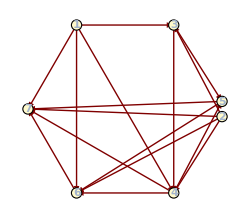
-Graphics--Graphics-

X_1[1,7]·X_1[7,6]·X_1[6,1] -1-a+X_1[2,6]·X_1[6,4]·X_1[4,2] -1-a+X_1[3,4]·X_1[4,5]·X_1[5,3] -1-a+X_1[5,6]·X_1[6,7]·X_1[7,5] -1-a+X_1[1,4]·X_1[4,7]·X_1[7,2]·X_1[2,3]·X_1[3,1] -1-a+X_1[2,3]·X_1[3,4]·X_1[4,2] 1+a+X_1[2,6]·X_1[6,7]·X_1[7,2] 1+a+X_1[4,7]·X_1[7,6]·X_1[6,4] 1+a+X_1[1,4]·X_1[4,5]·X_1[5,6]·X_1[6,1] 1+a+X_1[1,7]·X_1[7,5]·X_1[5,3]·X_1[3,1] 1+a

```mathematica
Row[{
QuiverGraph[{{2,5},3,1,7,6,4},QuiverFromFields@WPdP4aPhaseB],
(WPdP4aBFromDef3/.ChangeGroupIndices[{7,1,2,3,4,5,6}])//QuiverGraph[{{2,5},3,1,7,6,4},#]&
}]
a W[PdP4aPhaseB]+(WPdP4aBFromDef3/.ChangeGroupIndices[{7,1,2,3,4,5,6}])//Expand@Collect[Expand@Simplify@#,_CenterDot,Highlighted]&
```

## Mesonic Branch

### Model 5: PdP_(4b)

```mathematica
PdP4bFieldGenRules0=ToGeneratorVariableRules@GaugeInvariantMesons[QuiverFromFields@WPdP4b,5];
```

```mathematica
PdP4bFieldGenRules=ReduceGenerators[WPdP4b,Keys@PdP4bFieldGenRules0,PdP4bFieldGenRules0,"RemoveDenominators"->True]//KeyDrop[#,Cases[#,HoldPattern[Rule][f_,_Times]:>f]]&//KeyValueMap[Rule];
PdP4bFieldGenRules//Column
```

Abelianize::warn: Abelianization of the fields was done.

X_1[6,2]·X_1[2,6]→A[1]
X_1[1,7]·X_1[7,1]→A[2]
X_1[6,4]·X_1[4,5]·X_1[5,6]→B[1]
X_1[6,4]·X_1[4,2]·X_1[2,6]→B[1]
X_1[6,2]·X_1[2,5]·X_1[5,6]→B[1]
X_1[6,7]·X_1[7,5]·X_1[5,6]→B[4]
X_1[6,7]·X_1[7,2]·X_1[2,6]→B[1]
X_1[3,4]·X_1[4,5]·X_1[5,3]→B[6]
X_1[3,7]·X_1[7,5]·X_1[5,3]→B[1]
X_1[1,7]·X_1[7,5]·X_1[5,1]→B[1]
X_1[1,7]·X_1[7,2]·X_1[2,1]→B[1]
X_1[1,6]·X_1[6,2]·X_1[2,1]→B[1]
X_1[1,6]·X_1[6,7]·X_1[7,1]→B[1]
X_1[1,3]·X_1[3,7]·X_1[7,1]→B[1]
X_1[6,4]·X_1[4,2]·X_1[2,5]·X_1[5,6]→C[2]
X_1[6,7]·X_1[7,2]·X_1[2,5]·X_1[5,6]→C[2]
X_1[3,4]·X_1[4,2]·X_1[2,5]·X_1[5,3]→B[1]
X_1[3,7]·X_1[7,2]·X_1[2,5]·X_1[5,3]→C[4]
X_1[1,7]·X_1[7,2]·X_1[2,5]·X_1[5,1]→C[4]
X_1[1,6]·X_1[6,4]·X_1[4,5]·X_1[5,1]→C[4]
X_1[1,6]·X_1[6,4]·X_1[4,2]·X_1[2,1]→C[2]
X_1[1,6]·X_1[6,2]·X_1[2,5]·X_1[5,1]→C[4]
X_1[1,6]·X_1[6,7]·X_1[7,5]·X_1[5,1]→C[2]
X_1[1,6]·X_1[6,7]·X_1[7,2]·X_1[2,1]→C[2]
X_1[1,3]·X_1[3,4]·X_1[4,5]·X_1[5,1]→B[1]
X_1[1,3]·X_1[3,4]·X_1[4,2]·X_1[2,1]→C[12]
X_1[1,3]·X_1[3,7]·X_1[7,5]·X_1[5,1]→C[2]
X_1[1,3]·X_1[3,7]·X_1[7,2]·X_1[2,1]→C[2]
X_1[1,6]·X_1[6,4]·X_1[4,2]·X_1[2,5]·X_1[5,1]→D[3]
X_1[1,6]·X_1[6,7]·X_1[7,2]·X_1[2,5]·X_1[5,1]→D[3]
X_1[1,3]·X_1[3,4]·X_1[4,2]·X_1[2,5]·X_1[5,1]→C[2]
X_1[1,3]·X_1[3,7]·X_1[7,2]·X_1[2,5]·X_1[5,1]→D[3]

```mathematica
PdP4bFieldChiralIdeal=Eliminate[Abelianize@Join[Thread[0==FTerms@WPdP4b],Equal@@@PdP4bFieldGenRules],FieldCases@WPdP4b]
```

A[1] B[1]==A[2] B[1]&&A[1] B[4]==A[2] B[4]&&B[1] B[6]==A[2] B[1]&&B[4] B[6]==A[2] B[4]&&A[1] C[2]==B[1]^2&&A[2] C[2]==B[1]^2&&B[6] C[2]==B[1]^2&&A[1] C[4]==A[2] C[4]&&B[4] C[4]==B[1] C[2]&&B[6] C[4]==A[2] C[4]&&A[1] C[12]==A[2] B[4]&&A[2] C[12]==A[2] B[4]&&B[1] C[12]==B[1] B[4]&&B[6] C[12]==A[2] B[4]&&C[2] C[12]==B[4] C[2]&&C[4] C[12]==B[1] C[2]&&A[1] D[3]==B[1] C[4]&&A[2] D[3]==B[1] C[4]&&B[1] D[3]==C[2] C[4]&&B[4] D[3]==C[2]^2&&B[6] D[3]==B[1] C[4]&&C[12] D[3]==C[2]^2

```mathematica
PdP4bFieldMesonicIdeal=Eliminate[B[4]==C[12]&&A[2]==B[6]&&A[1]==B[6]&&PdP4bFieldChiralIdeal,{C[12],B[6],A[2]}]
```

A[1] C[2]==B[1]^2&&B[4] C[4]==B[1] C[2]&&A[1] D[3]==B[1] C[4]&&B[1] D[3]==C[2] C[4]&&B[4] D[3]==C[2]^2

### Model 6: PdP_(4a) (a)

```mathematica
PdP4aFieldGenRules0=ToGeneratorVariableRules@GaugeInvariantMesons[QuiverFromFields@WPdP4aPhaseA,5];
```

```mathematica
PdP4aFieldGenRules=ReduceGenerators[WPdP4aPhaseA,Keys@PdP4aFieldGenRules0,PdP4aFieldGenRules0,"RemoveDenominators"->True]//KeyDrop[#,Cases[#,HoldPattern[Rule][f_,_Times]:>f]]&//KeyValueMap[Rule];
PdP4aFieldGenRules//Column
```

Abelianize::warn: Abelianization of the fields was done.

X_1[7,6]·X_1[6,2]·X_1[2,7]→B[1]
X_1[7,3]·X_1[3,2]·X_1[2,7]→C[1]
X_1[1,7]·X_1[7,6]·X_1[6,1]→C[1]
X_1[1,7]·X_1[7,3]·X_1[3,1]→B[4]
X_1[7,5]·X_1[5,6]·X_1[6,2]·X_1[2,7]→C[1]
X_1[7,5]·X_1[5,3]·X_1[3,2]·X_1[2,7]→C[2]
X_1[4,5]·X_1[5,6]·X_1[6,2]·X_1[2,4]→C[3]
X_1[4,5]·X_1[5,3]·X_1[3,2]·X_1[2,4]→C[1]
X_1[4,7]·X_1[7,6]·X_1[6,2]·X_1[2,4]→C[1]
X_1[4,7]·X_1[7,3]·X_1[3,2]·X_1[2,4]→D[1]
X_1[1,7]·X_1[7,5]·X_1[5,6]·X_1[6,1]→D[1]
X_1[1,7]·X_1[7,5]·X_1[5,3]·X_1[3,1]→C[1]
X_1[1,4]·X_1[4,5]·X_1[5,6]·X_1[6,1]→C[1]
X_1[1,4]·X_1[4,5]·X_1[5,3]·X_1[3,1]→C[10]
X_1[1,4]·X_1[4,7]·X_1[7,6]·X_1[6,1]→C[2]
X_1[1,4]·X_1[4,7]·X_1[7,3]·X_1[3,1]→C[1]
X_1[4,7]·X_1[7,5]·X_1[5,6]·X_1[6,2]·X_1[2,4]→D[1]
X_1[4,7]·X_1[7,5]·X_1[5,3]·X_1[3,2]·X_1[2,4]→D[2]
X_1[1,4]·X_1[4,7]·X_1[7,5]·X_1[5,6]·X_1[6,1]→D[2]
X_1[1,4]·X_1[4,7]·X_1[7,5]·X_1[5,3]·X_1[3,1]→C[2]

```mathematica
PdP4aFieldChiralIdeal=Eliminate[Abelianize@Join[Thread[0==FTerms@W@PdP4aPhaseA],Equal@@@PdP4aFieldGenRules],FieldCases@WPdP4aPhaseA]
```

B[4] C[2]==C[1]^2&&B[1] C[3]==B[1] B[4]&&C[1] C[3]==B[4] C[1]&&C[2] C[3]==C[1]^2&&B[4] C[10]==B[1] B[4]&&C[1] C[10]==B[1] C[1]&&C[2] C[10]==B[1] C[2]&&C[3] C[10]==B[1] B[4]&&B[1] D[1]==C[1]^2&&C[3] D[1]==B[4] D[1]&&C[10] D[1]==C[1]^2&&B[1] D[2]==C[1] C[2]&&B[4] D[2]==C[1] D[1]&&C[1] D[2]==C[2] D[1]&&C[3] D[2]==C[1] D[1]&&C[10] D[2]==C[1] C[2]

```mathematica
PdP4aFieldMesonicIdeal=First@PrimaryDecompositionM2[PdP4aFieldChiralIdeal,UniqueCases[PdP4aFieldChiralIdeal,$GeneratorVars[_]]]//GroupBy[#,MinMaxExponent[$GeneratorVars[_]]]&//(And@@Simplify@Thread[0==#[{2,2}]]/.Echo@If[MissingQ@(#[{1,1}]),{},First@Quiet@Solve[#[{1,1}]==0]]&)
```

{C[3]→B[4],C[10]→B[1]}

C[1] D[1]==B[4] D[2]&&C[2] D[1]==C[1] D[2]&&B[4] C[2]==B[1] D[1]&&C[1]^2==B[1] D[1]&&C[1] C[2]==B[1] D[2]

### PdP_(4b) ⟹ PdP_(4a) (a)

#### Deformation 1: (1→7→1) – (2→6→2)

```mathematica
PdP4bDef1FieldGenRules=ReduceGenerators[WPdP4bDef1,Keys@PdP4bFieldGenRules,PdP4bFieldGenRules0,"RemoveDenominators"->True]
```

Abelianize::warn: Abelianization of the fields was done.

{X_1[6,2]·X_1[2,6]→A[1],X_1[1,7]·X_1[7,1]→A[1],X_1[6,4]·X_1[4,5]·X_1[5,6]→B[1],X_1[6,4]·X_1[4,2]·X_1[2,6]→B[1],X_1[6,2]·X_1[2,5]·X_1[5,6]→B[1],X_1[6,7]·X_1[7,5]·X_1[5,6]→B[4],X_1[6,7]·X_1[7,2]·X_1[2,6]→-m A[1]+B[1],X_1[3,4]·X_1[4,5]·X_1[5,3]→B[6],X_1[3,7]·X_1[7,5]·X_1[5,3]→B[1],X_1[1,7]·X_1[7,5]·X_1[5,1]→B[1],X_1[1,7]·X_1[7,2]·X_1[2,1]→-m A[1]+B[1],X_1[1,6]·X_1[6,2]·X_1[2,1]→-m A[1]+B[1],X_1[1,6]·X_1[6,7]·X_1[7,1]→-m A[1]+B[1],X_1[1,3]·X_1[3,7]·X_1[7,1]→B[1],X_1[6,4]·X_1[4,2]·X_1[2,5]·X_1[5,6]→m B[1]+C[2],X_1[6,7]·X_1[7,2]·X_1[2,5]·X_1[5,6]→C[2],X_1[3,4]·X_1[4,2]·X_1[2,5]·X_1[5,3]→B[1],X_1[3,7]·X_1[7,2]·X_1[2,5]·X_1[5,3]→C[4],X_1[1,7]·X_1[7,2]·X_1[2,5]·X_1[5,1]→C[4],X_1[1,6]·X_1[6,4]·X_1[4,5]·X_1[5,1]→C[4],X_1[1,6]·X_1[6,4]·X_1[4,2]·X_1[2,1]→C[2],X_1[1,6]·X_1[6,2]·X_1[2,5]·X_1[5,1]→C[4],X_1[1,6]·X_1[6,7]·X_1[7,5]·X_1[5,1]→C[2],X_1[1,6]·X_1[6,7]·X_1[7,2]·X_1[2,1]→m^2 A[1]-m B[1]+C[2],X_1[1,3]·X_1[3,4]·X_1[4,5]·X_1[5,1]→B[1],X_1[1,3]·X_1[3,4]·X_1[4,2]·X_1[2,1]→C[12],X_1[1,3]·X_1[3,7]·X_1[7,5]·X_1[5,1]→m B[1]+C[2],X_1[1,3]·X_1[3,7]·X_1[7,2]·X_1[2,1]→C[2],X_1[1,6]·X_1[6,4]·X_1[4,2]·X_1[2,5]·X_1[5,1]→m C[4]+D[3],X_1[1,6]·X_1[6,7]·X_1[7,2]·X_1[2,5]·X_1[5,1]→D[3],X_1[1,3]·X_1[3,4]·X_1[4,2]·X_1[2,5]·X_1[5,1]→m B[1]+C[2],X_1[1,3]·X_1[3,7]·X_1[7,2]·X_1[2,5]·X_1[5,1]→m C[4]+D[3]}

```mathematica
PdP4bDef1FieldChiralIdeal=Eliminate[Abelianize@Join[Equal@@@PdP4bDef1FieldGenRules,Thread[FTerms@WPdP4bDef1==0]],FieldCases@WPdP4bDef1]
```

B[1] B[6]==A[1] B[1]&&B[4] B[6]==A[1] B[4]&&A[1] C[2]==B[1] (-m A[1]+B[1])&&B[6] C[2]==B[1] (-m A[1]+B[1])&&B[4] C[4]==B[1] C[2]&&B[6] C[4]==A[1] C[4]&&A[1] C[12]==A[1] B[4]&&B[1] C[12]==B[1] B[4]&&B[6] C[12]==A[1] B[4]&&C[2] C[12]==B[4] C[2]&&C[4] C[12]==B[1] C[2]&&A[1] D[3]==(-m A[1]+B[1]) C[4]&&B[1] D[3]==C[2] C[4]&&B[4] D[3]==C[2]^2&&B[6] D[3]==(-m A[1]+B[1]) C[4]&&C[12] D[3]==C[2]^2

```mathematica
PdP4bDef1FieldChiralIdealNew=Join[
List@@PdP4bDef1FieldChiralIdeal,
MapIndexed[#1==Y@First@#2&,Keys@GroupBy[PdP4bDef1FieldGenRules,Last->First]⟦{3,5,6,7,9,10,11,12}⟧]
]//ReplaceAll[{Y[2]->(Y[2]+Y[3]-2 Y[4])/m^2}]//Eliminate[#,Sort@UniqueCases[#,($GeneratorVars)[__]]]&//Simplify[#,m>0]&
```

Y[1] Y[2]==Y[5] Y[6]&&Y[1] Y[3]==Y[3] Y[6]&&Y[2] Y[3]==Y[4]^2&&Y[1] Y[4]==Y[4] Y[6]&&Y[2] Y[4]==Y[4] Y[5]&&Y[1] Y[5]==Y[5] Y[6]&&Y[4]^2==Y[3] Y[5]&&Y[2] Y[6]==Y[5] Y[6]&&Y[3] Y[4]==Y[1] Y[7]&&Y[2] Y[7]==Y[4] Y[8]&&Y[4] Y[7]==Y[3] Y[8]&&Y[5] Y[7]==Y[4] Y[8]&&Y[3] Y[4]==Y[6] Y[7]&&Y[4]^2==Y[1] Y[8]&&Y[2] Y[8]==Y[5] Y[8]&&Y[4]^2==Y[6] Y[8]

```mathematica
PdP4bDef1FieldChiralIdealOther=Join[
List@@PdP4bDef1FieldChiralIdeal,
MapIndexed[#1==Y@First@#2&,Keys@GroupBy[PdP4bDef1FieldGenRules,Last->First]⟦{3,5,6,7,9,10,11,12}⟧]
]//ReplaceAll[{Y[2]->(Y[2]+Y[5]-2 Y[4])/m^2}]//Eliminate[#,Sort@UniqueCases[#,($GeneratorVars)[__]]]&//Simplify[#,m>0]&
```

Y[1] Y[2]==Y[2] Y[6]&&Y[1] Y[3]==Y[2] Y[6]&&Y[3]^2==Y[2] Y[3]&&Y[1] Y[4]==Y[4] Y[6]&&Y[2] Y[4]==Y[6] Y[7]&&Y[3] Y[4]==Y[6] Y[7]&&Y[1] Y[5]==Y[5] Y[6]&&Y[4]^2==Y[3] Y[5]&&Y[3] Y[6]==Y[2] Y[6]&&Y[2] Y[5] Y[6]==Y[4]^2 Y[6]&&Y[1] Y[7]==Y[6] Y[7]&&Y[3] Y[7]==Y[2] Y[7]&&Y[5] Y[7]==Y[4] Y[8]&&Y[4]^2==Y[1] Y[8]&&Y[4] Y[7]==Y[2] Y[8]&&Y[4] Y[7]==Y[3] Y[8]&&Y[4]^2==Y[6] Y[8]

```mathematica
First@PrimaryDecompositionM2[PdP4bDef1FieldChiralIdealNew,Y/@Range[8]]//Eliminate[0==#,{Y[5],Y[6]}]&
```

Y[2] Y[3]==Y[4]^2&&Y[1] Y[7]==Y[3] Y[4]&&Y[2] Y[7]==Y[4] Y[8]&&Y[1] Y[8]==Y[4]^2&&Y[3] Y[8]==Y[4] Y[7]

```mathematica
PrimaryDecompositionM2[PdP4bDef1FieldChiralIdealOther,Y/@Range[8]]//Eliminate[0==First@#,{Y[3],Y[6]}]&
```

Y[2] Y[4]==Y[1] Y[7]&&Y[2] Y[5]==Y[4]^2&&Y[5] Y[7]==Y[4] Y[8]&&Y[1] Y[8]==Y[4]^2&&Y[2] Y[8]==Y[4] Y[7]

```mathematica
PdP4bDef1FieldMesonicIdeal=Eliminate[C[12]==B[4]&&B[6]==A[1]&&PdP4bDef1FieldChiralIdeal,{C[12],B[6]}]
PdP4bDef1FieldMesGenRules=(PdP4bDef1FieldGenRules//ReplaceAll[{C[12]->B[4],B[6]->A[1]}]);
```

m A[1] B[1]==B[1]^2-A[1] C[2]&&B[4] C[4]==B[1] C[2]&&A[1] D[3]==(-m A[1]+B[1]) C[4]&&B[1] D[3]==C[2] C[4]&&B[4] D[3]==C[2]^2

```mathematica
PdP4bDef1FieldMesonicIdealNew=Join[
List@@PdP4bDef1FieldMesonicIdeal,
MapIndexed[#1==Z@First@#2&,Keys@GroupBy[PdP4bDef1FieldMesGenRules,Last->First]⟦{3,5,6,8,9,10}⟧]
]//Eliminate[#,Sort@UniqueCases[#,($GeneratorVars)[__]]]&
```

Z[2] Z[4]==Z[3]^2&&Z[1] Z[5]==Z[2] Z[3]&&Z[1] Z[6]==Z[3]^2&&Z[2] Z[6]==Z[3] Z[5]&&Z[3] Z[6]==Z[4] Z[5]

```mathematica
redef1=Thread[{B[4],B[6],B[1],C[2],A[1],C[12],C[4],D[3]}-> {B[4],(-2 B[1]+B[6]+C[2])/m^2,(A[1]-B[1])/m,B[1],(A[1]-2 B[1]+C[2])/m^2,C[12],(C[4]-D[3])/m,D[3]}];
redef2=Thread[{B[4],B[6],B[1],C[2],A[1],C[12],C[4],D[3]}-> {B[4],(B[1]+B[6]-2 C[2])/m^2,(B[1]-C[2])/m,C[2],(A[1]+B[1]-2 C[2])/m^2,C[12],(C[4]-D[3])/m,D[3]}];
```

## Resolutions flow

### PdP_(4b)

```mathematica
kcCompTbPdP4b=DataCheck[
KahlerChambersCompatibility[WPdP4b,"ShowProgress"->True],
"kcCompTb_PdP4b.wl"
];
```

### PdP_(4a) (a)

#### From deformation 1: (1→7→1) – (2→6→2)

```mathematica
kcCompTbPdP4aA=DataCheck[
KahlerChambersCompatibility[WPdP4aAFromDef1,"ShowProgress"->True],
"kcCompTb_PdP4aA.wl"
];
```

#### From deformation 3: (2→6→2) – (3→4→5→3)

```mathematica
kcCompTbPdP4aB=DataCheck[
KahlerChambersCompatibility[WPdP4aBFromDef3,"ShowProgress"->True],
"kcCompTb_PdP4aB.wl"
];
```

### PdP_(4b) ⟹ PdP_(4a) (a)

#### Deformation 1: (1→7→1) – (2→6→2)

```mathematica
kcFlowPdP4bPdP4aA=DataCheck[
KahlerChambersFlowGraph[kcCompTbPdP4b,kcCompTbPdP4aA,"ShowProgress"->True],
"kcFlow_PdP4b_PdP4aA.wl"
];
```

```mathematica
equalGraphPdP4bPdP4aA=Apply[UndirectedEdge]@*VertexList/@Select[IsomorphicGraphQ[CycleGraph[2,DirectedEdges->True],#]&]@WeaklyConnectedGraphComponents@kcFlowPdP4bPdP4aA;
nonequalGraphPdP4bPdP4aA=Select[Not@IsomorphicGraphQ[CycleGraph[2,DirectedEdges->True],#]&]@WeaklyConnectedGraphComponents@kcFlowPdP4bPdP4aA;
```

```mathematica
Graph[#,GraphLayout->"LayeredEmbedding"]&/@Join[
GroupBy[EdgeList@Graph[Splice@*EdgeList/@nonequalGraphPdP4bPdP4aA],
MapAt[{pqWebPlot[TransformedMesh[{{0,1},{-1,0}}]@#,ImageSize->{Automatic,150}, Frame->True, FrameTicks->None],pqWebPlot[TransformedMesh[{{0,1},{-1,-1}}]@#,ImageSize->{Automatic,150}, Frame->True, FrameTicks->None]}&,{2}]@*MapAt[(pqWebPlot[#,ImageSize->{Automatic,150},Frame->True, FrameTicks->None]&),{1}]@*Apply[DirectedEdge]@*Map[First]->Apply[DirectedEdge]@*Map[Last]
],
GroupBy[EdgeList@equalGraphPdP4bPdP4aA,
MapAt[{pqWebPlot[TransformedMesh[{{0,1},{-1,0}}]@#,ImageSize->{Automatic,150}, Frame->True, FrameTicks->None],pqWebPlot[TransformedMesh[{{0,1},{-1,-1}}]@#,ImageSize->{Automatic,150}, Frame->True, FrameTicks->None]}&,{2}]@*MapAt[(pqWebPlot[#,ImageSize->{Automatic,150}, Frame->True, FrameTicks->None]&),{1}]@*Sort@*Apply[UndirectedEdge]@*Map[First]->Apply[UndirectedEdge]@*Map[Last]
]
]//Grid[KeyValueMap[List]@#,Frame->All,ItemSize->{{All,Automatic},Automatic}]&;
Export[FileNameJoin[{$FiguresDirectory,"kcFlowGraph_PdP4b_PdP4aA.pdf"}],%]
```

/Users/jose/Library/CloudStorage/Dropbox/zig-zag-deformation-data/Rank1-Reflexive/figures/kcFlowGraph_PdP4b_PdP4aA.pdf

### PdP_(4b) ⟹ PdP_(4a) (b)

#### Deformation 3: (2→6→2) – (3→4→5→3)

```mathematica
kcFlowPdP4bPdP4aB=DataCheck[
KahlerChambersFlowGraph[kcCompTbPdP4b,kcCompTbPdP4aB,"ShowProgress"->True],
"kcFlow_PdP4b_PdP4aB.wl"
];
```

```mathematica
equalGraphPdP4bPdP4aB=Apply[UndirectedEdge]@*VertexList/@Select[IsomorphicGraphQ[CycleGraph[2,DirectedEdges->True],#]&]@WeaklyConnectedGraphComponents@kcFlowPdP4bPdP4aB;
nonequalGraphPdP4bPdP4aB=Select[Not@IsomorphicGraphQ[CycleGraph[2,DirectedEdges->True],#]&]@WeaklyConnectedGraphComponents@kcFlowPdP4bPdP4aB;
```

```mathematica
Graph[#,GraphLayout->"LayeredEmbedding"]&/@Join[
GroupBy[EdgeList@Graph[Splice@*EdgeList/@nonequalGraphPdP4bPdP4aB],
MapAt[{pqWebPlot[TransformedMesh[{{0,1},{-1,0}}]@#,ImageSize->{Automatic,150}, Frame->True, FrameTicks->None],pqWebPlot[TransformedMesh[{{0,1},{-1,-1}}]@#,ImageSize->{Automatic,150}, Frame->True, FrameTicks->None]}&,{2}]@*MapAt[(pqWebPlot[#,ImageSize->{Automatic,150}, Frame->True, FrameTicks->None]&),{1}]@*Apply[DirectedEdge]@*Map[First]->Apply[DirectedEdge]@*Map[Last]
],
GroupBy[EdgeList@equalGraphPdP4bPdP4aB,
MapAt[{pqWebPlot[TransformedMesh[{{0,1},{-1,0}}]@#,ImageSize->{Automatic,150}, Frame->True, FrameTicks->None],pqWebPlot[TransformedMesh[{{0,1},{-1,-1}}]@#,ImageSize->{Automatic,150}, Frame->True, FrameTicks->None]}&,{2}]@*MapAt[(pqWebPlot[#,ImageSize->{Automatic,150}, Frame->True, FrameTicks->None]&),{1}]@*Sort@*Apply[UndirectedEdge]@*Map[First]->Apply[UndirectedEdge]@*Map[Last]
]
]//Grid[KeyValueMap[List]@#,Frame->All,ItemSize->{{All,Automatic},Automatic}]&;
Export[FileNameJoin[{$FiguresDirectory,"kcFlowGraph_PdP4b_PdP4aB.pdf"}],%]
```

/Users/jose/Library/CloudStorage/Dropbox/zig-zag-deformation-data/figures/kcFlowGraph_PdP4b_PdP4aB.pdf

## Resolutions volumes

### PdP_(4b) ⟹ PdP_(4a) (a)

#### Deformation 1: (1→7→1) – (2→6→2)

```mathematica
kvTbPdP4b=DataCheck[
KahlerVolumes[W@PdP4b,"ShowProgress"-> True],
"kvTb_PdP4b.wl"
];
```

```mathematica
kvTbPdP4aA=DataCheck[
KahlerVolumes[WPdP4aAFromDef1,"ShowProgress"-> True],
"kvTb_PdP4aA.wl"
];
```

```mathematica
tM={{0,1},{-1,0}};
polytVolPdP4bPdP4aA=volumesTable[
MapAt[KeyMap[x↦tM.x],{All,-1,2}]@MapAt[TransformedMesh[tM],{All,-1,1}]@Map[SortBy@First]@WeaklyConnectedComponents[kcFlowPdP4bPdP4aB],
{kvTbPdP4b,Map[
KeyMap[KeyMap[x↦tM.x]]@*Map[KeyMap[x↦x.Transpose[tM]]],
KeyMap[TransformedMesh[tM]]@kvTbPdP4aA]}
];
```

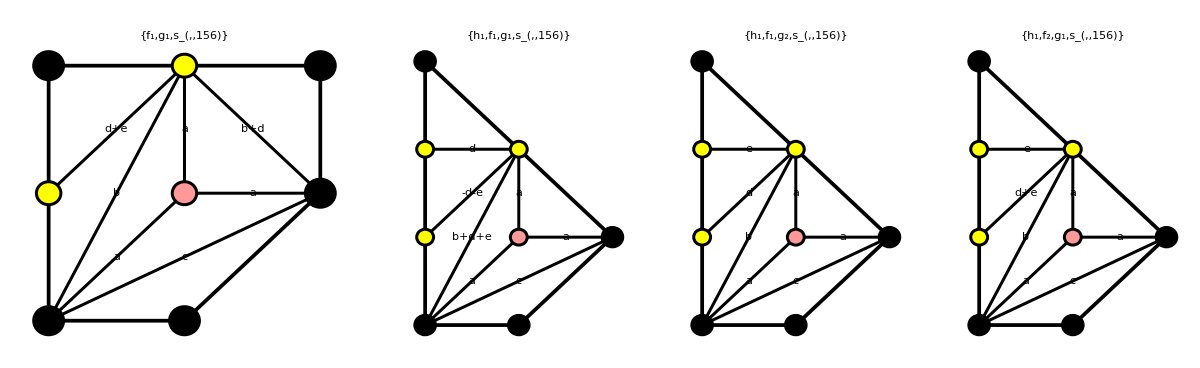
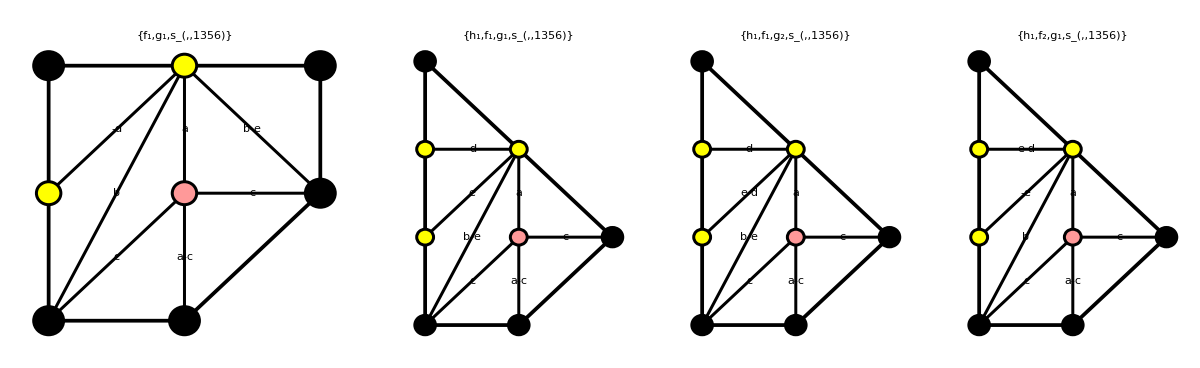
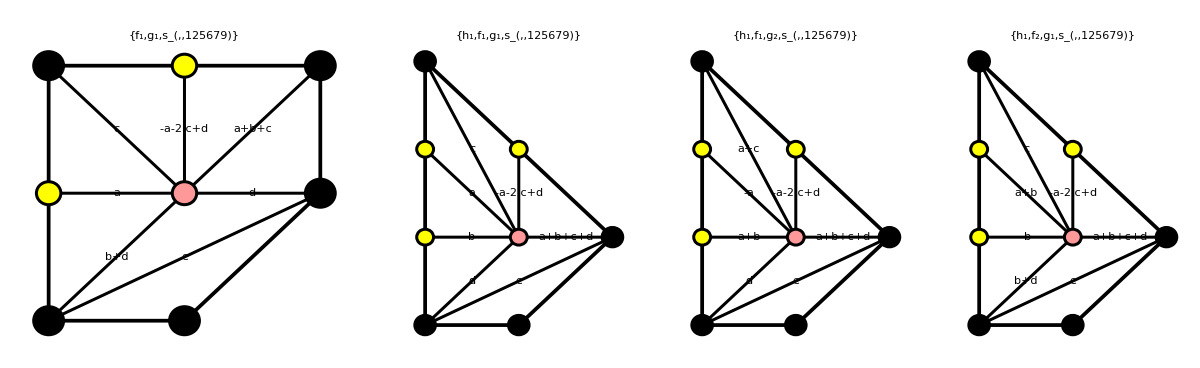
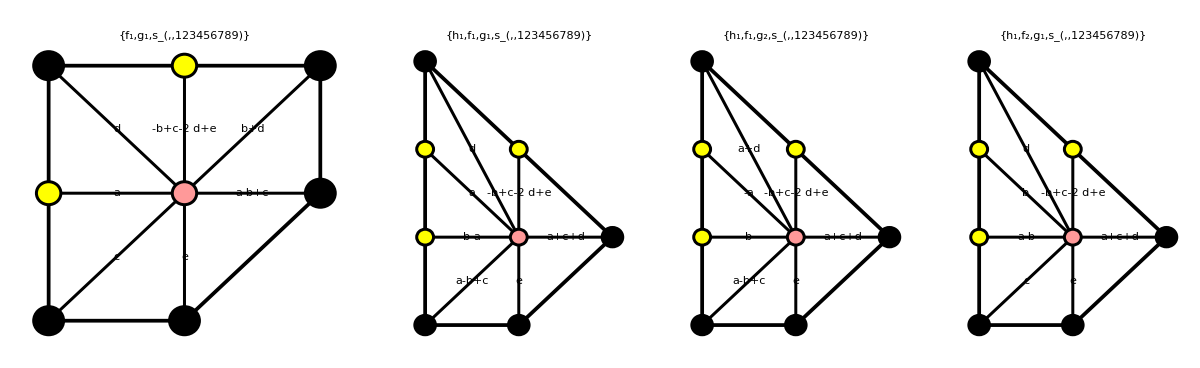
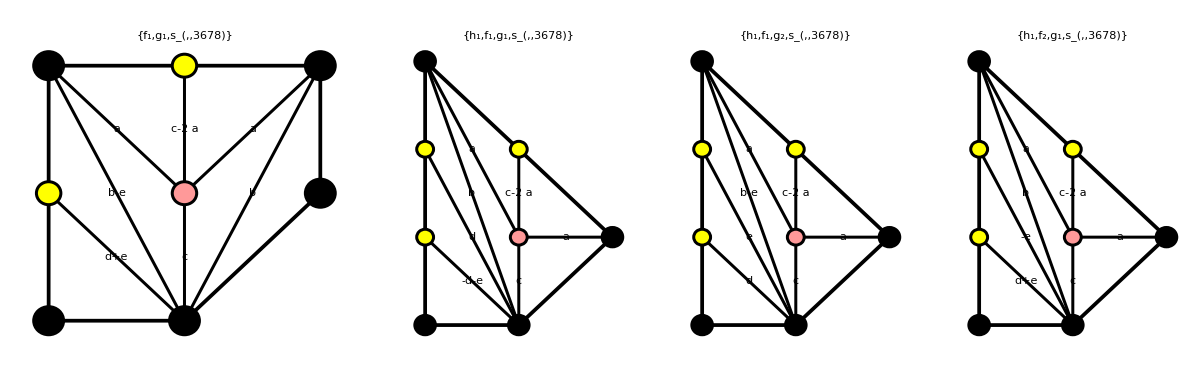
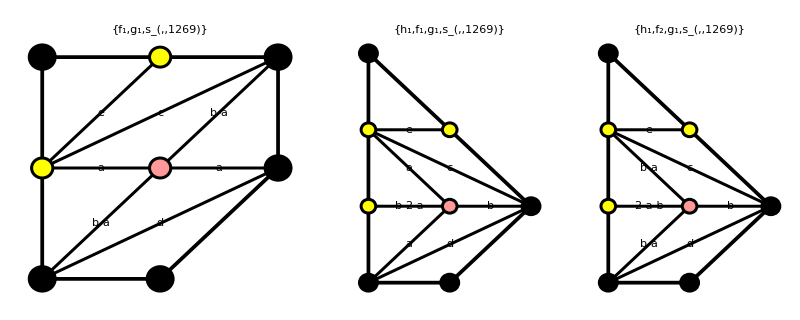
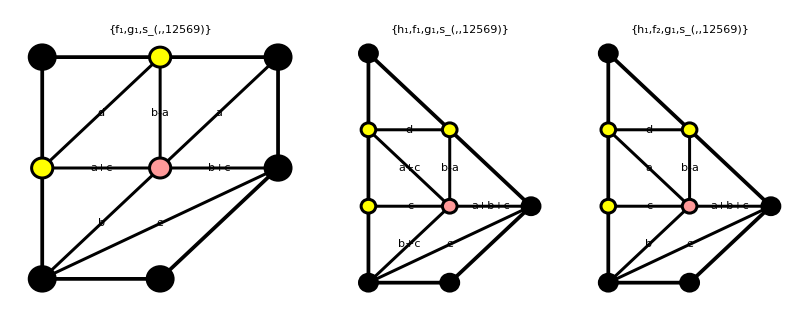
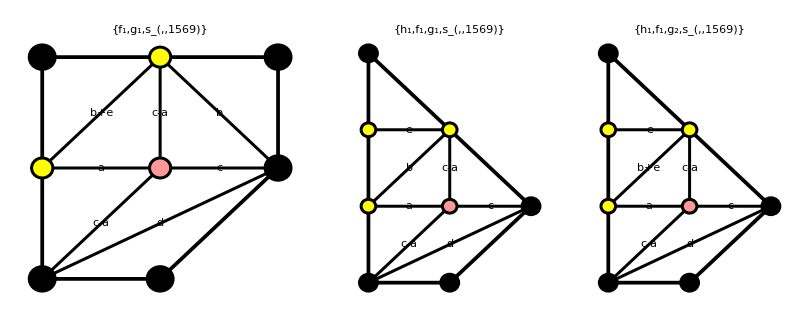

```mathematica
KeyValueMap[
{k,v}↦MapThread[PolytopePlot[#1,"PolytopeCellLabel"->Normal[(Style[#,Background->LightBlue]&)/@#2],PlotLabel->#3]&,{Splice@Transpose@k,First@v}],
polytVolPdP4bPdP4aA
]//ReverseSortBy[Length]//Map[GraphicsRow]//Column
```

### PdP_(4b) ⟹ PdP_(4a) (b)

#### Deformation 3: (2→6→2) – (3→4→5→3)

```mathematica
kvTbPdP4aB=DataCheck[
KahlerVolumes[WPdP4aBFromDef3,"ShowProgress"-> True],
"kvTb_PdP4aB.wl"
];
```

```mathematica
tM={{0,1},{-1,0}};
polytVolPdP4bPdP4aB=volumesTable[
MapAt[KeyMap[x↦tM.x],{All,-1,2}]@MapAt[TransformedMesh[tM],{All,-1,1}]@Map[SortBy@First]@WeaklyConnectedComponents[kcFlowPdP4bPdP4aB],
{kvTbPdP4b,Map[
KeyMap[KeyMap[x↦tM.x]]@*Map[KeyMap[x↦x.Transpose[tM]]],
KeyMap[TransformedMesh[tM]]@kvTbPdP4aB]}
];
```

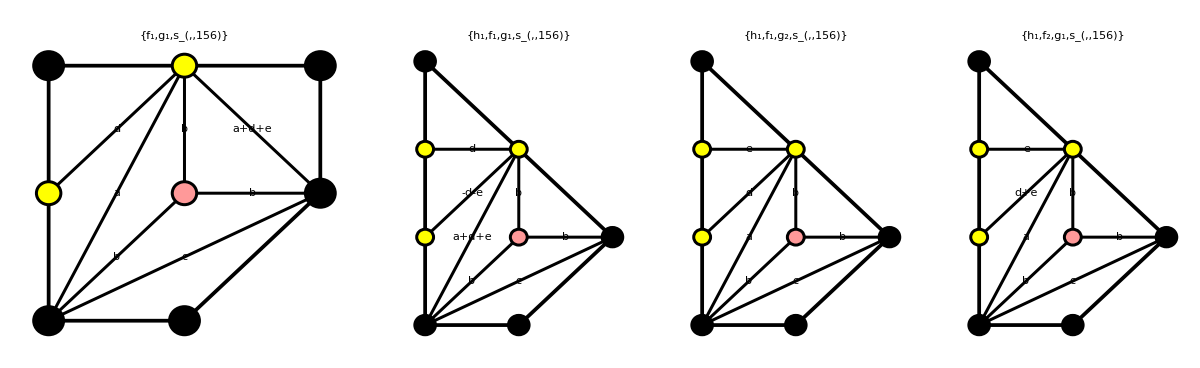
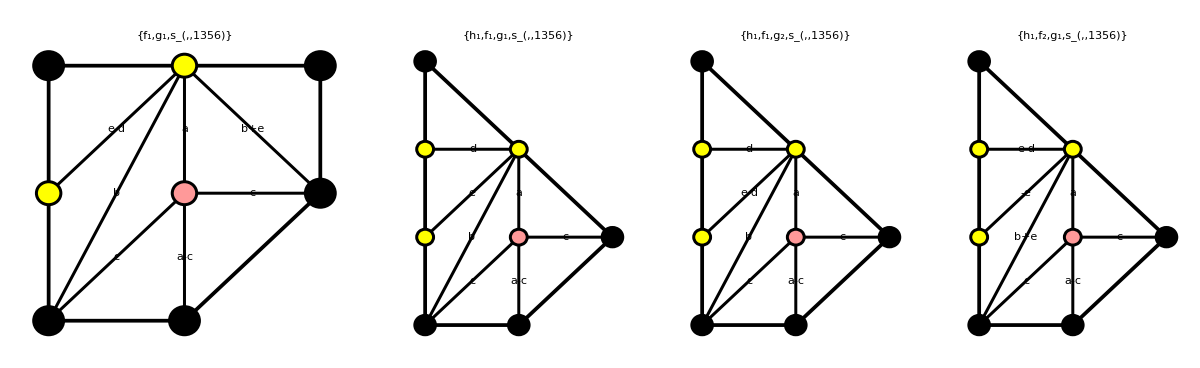
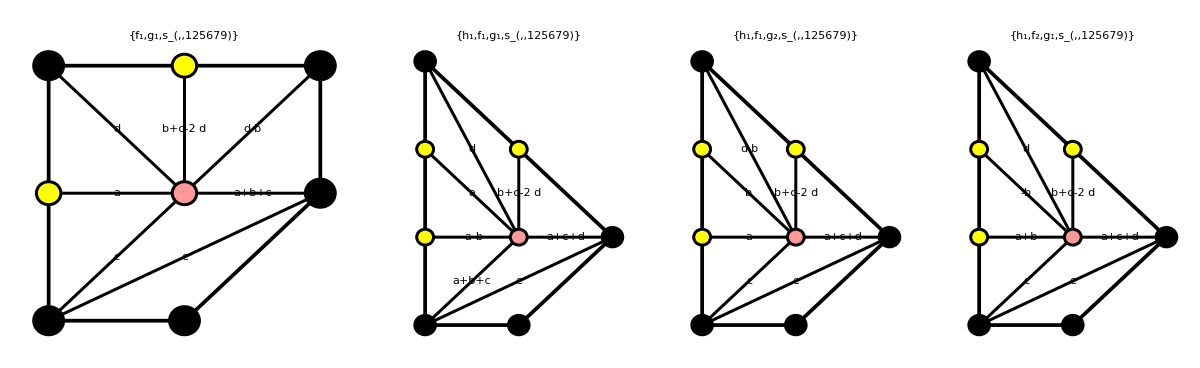
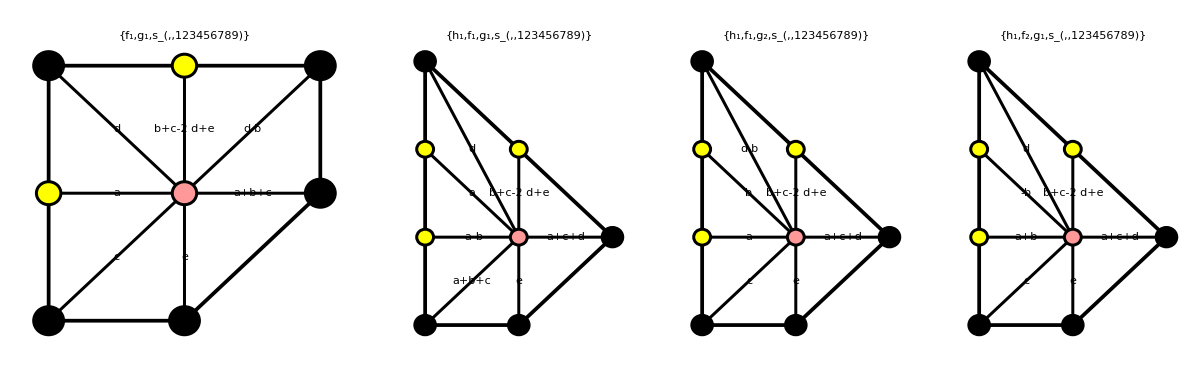
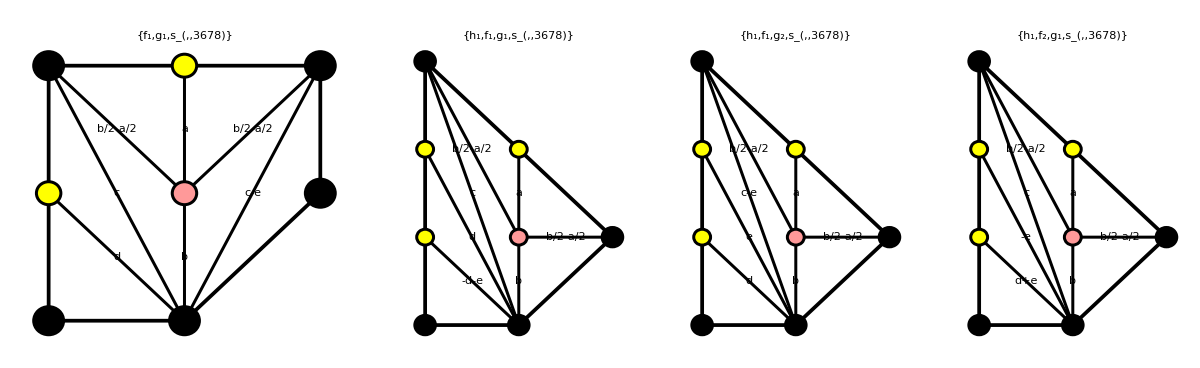
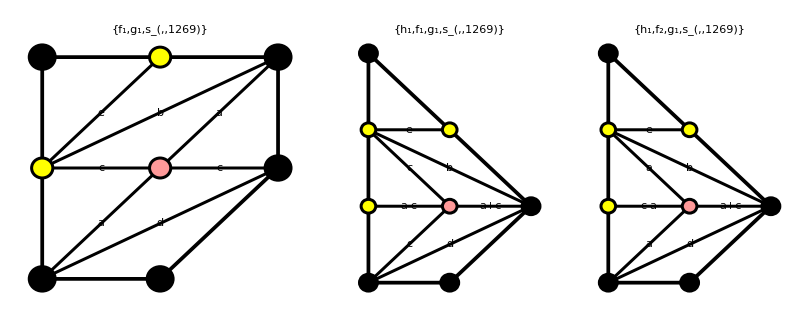
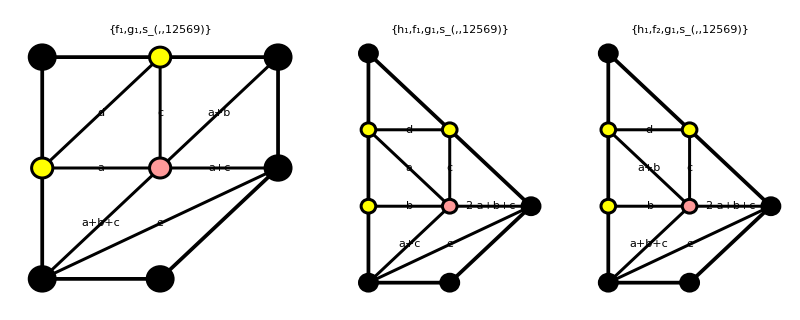
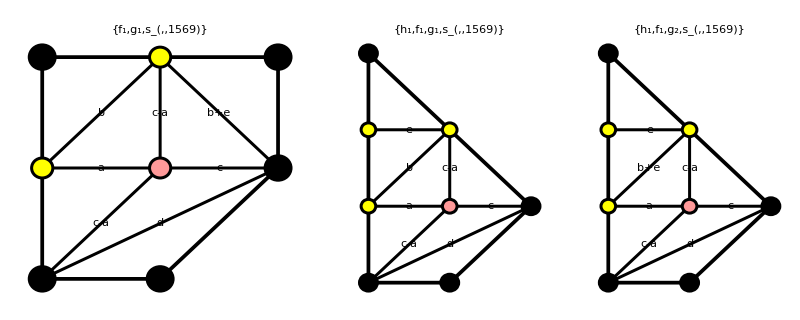
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-

```mathematica
KeyValueMap[
{k,v}↦MapThread[PolytopePlot[#1,"PolytopeCellLabel"->Normal[(Style[#,Background->LightBlue]&)/@#2],PlotLabel->#3]&,{Splice@Transpose@k,First@v}],
polytVolPdP4bPdP4aB
]//ReverseSortBy[Length]//Map[GraphicsRow]//Column
```